# House-of-cards approximation for ancestral equilibrium

## attempt #1 - ignore

First define the mutational kernel g and fitness function w (here in 2-dimensions):

```mathematica
g[x1_,x2_]:=(ⅇ^(1/2 (-x1^2/λ-x2^2/λ)))/(2 π λ)
w[x1_,x2_]:=ⅇ^(1/2 (-x1^2-x2^2))
```

where λ is the variance in mutational effect in each dimension and x1 and x2 are the trait values in each dimension.

Then at equilibrium, under the house-of-cards (HoC) approximation, the distribution of trait values is (Turelli 1984 eqn 3.2a)

```mathematica
p[x1,x2]==(μ g[x1,x2])/(1-k w[x1,x2])/.k->(1-μ)/Integrate[p[x1,x2]w[x1,x2],{x1,-∞,∞},{x2,-∞,∞}];
sol=Simplify[Solve[{%},p[x1,x2]],λ>0]
FullSimplify[%%/.%[[2]],{λ>0,1≥μ>0}]
%/.μ->0.001/.λ->0.005/.x1->1/.x2->2
```

{{p[x1,x2]→0},{p[x1,x2]→(ⅇ^(-((x1^2+x2^2) (1+λ))/(2 λ)) (-ⅇ^((x1^2+x2^2)/(2 λ)) λ (-1+μ)+ⅇ^(1/2 (x1^2+x2^2)) μ))/(2 π λ)}}

((-1+μ) (ⅇ^(((x1^2+x2^2) (1+λ))/(2 λ)) λ (-1+λ (-1+μ)-μ)+2 (1+λ) (-ⅇ^((x1^2+x2^2)/(2 λ)) λ (-1+μ)+ⅇ^(1/2 (x1^2+x2^2)) μ)))/(ⅇ^(1/2 (x1^2+x2^2)) (-1+λ (-1+μ)-μ)-2 (1+λ) (-1+μ))==0

False

Mathematica is not finding the right solution.

Let’s see if we can follow Turelli’s 1984 reasoning instead.

First note that we have the same equation, 3.2a, but in n dimensions instead of 1. So when n=1 we have the exact same results, namely when 3.8 holds, implying u<< m^2/Vs=α^2/(1/σ)=α^2 σ << 1, we have 3.9

```mathematica
g[x_]:=PDF[NormalDistribution[0,α],x]
w[x_]:=ⅇ^(-σ x^2/2)
p[x]==(u g[x])/(1-k w[x])/.k->Exp[-u^2 π /α^2];
sol=Simplify[Solve[{%},p[x]],α>0]//Flatten
FullSimplify[%%/.%,{α>0,1≥u>0}]
```

{p[x]→(ⅇ^((2 π u^2+x^2 (-1+α^2 σ))/(2 α^2)) u)/((-1+ⅇ^((π u^2)/α^2+(x^2 σ)/2)) √(2 π) α)}

True

Plot this equilibrium HoC distribution

{0.0001,0.001,1}

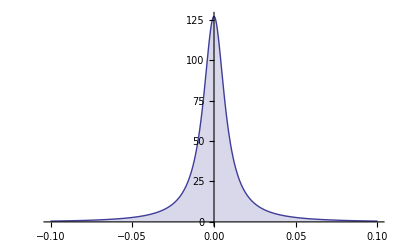

```mathematica
{u,α^2 σ,1}/.α->0.1/.u->0.0001/.σ->0.1
p[x]/.sol/.α->0.1/.u->0.0001/.σ->0.1;
Plot[%,{x,-0.1,0.1},PlotRange->All,Filling->0]
```

Compare with some simulations

```mathematica
SetDirectory[NotebookDirectory[]]; 
Table[xs[i]=Import["../scripts/data/z_m1_N10000_alpha0.1_u0.0001_sigma1.0_rep"<>ToString[i]<>".csv"]//Flatten,{i,10}];
allreps=Table[xs[i],{i,10}]//Flatten;
```

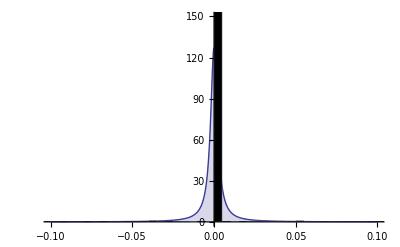

```mathematica
p[x]/.sol/.α->0.1/.u->0.0001/.σ->1;
Show[
Plot[%,{x,-0.1,0.1},PlotRange->{0,All},Filling->0],
Histogram[allreps,100,"PDF",ChartStyle->Black],
PlotRange->{{-0.1,0.1},{0,150}}
]
```

```mathematica
PDF[MultinormalDistribution[{0},IdentityMatrix[1]*α^2],x]
```

PDF[MultinormalDistribution[{0},{{α^2}}],x]

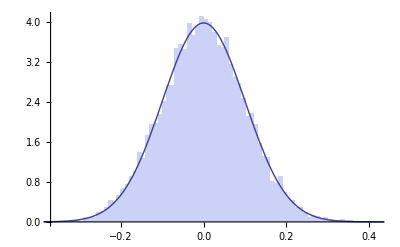

```mathematica
RandomVariate[MultinormalDistribution[{0},IdentityMatrix[1]*α^2]/.α->0.1,10000]//Flatten;
Show[
Histogram[%,100,"PDF"],
Plot[PDF[MultinormalDistribution[{0},IdentityMatrix[1]*α^2]/.α->0.1,{x}],{x,-0.5,0.5}]
]
```

```mathematica
CDF[MultinormalDistribution[{0},{{α^2}}],{x}]
(%/.x->0.25)-(%/.x->0.2)/.α->0.1
```

1/2 Erfc[-x/(√2 √(α^2))]

0.0165405

```mathematica
SetDirectory[NotebookDirectory[]]; 
Table[xs[i]=Import["../scripts/data/z_m1_N10000_alpha0.1_u0.0010_sigma1.0_rep"<>ToString[i]<>".csv"]//Flatten,{i,10}];
allreps=Table[xs[i],{i,10}]//Flatten;
```

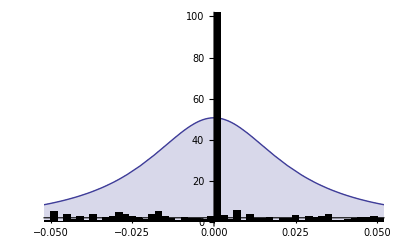

```mathematica
p[x]/.sol/.α->0.1/.u->0.001/.σ->1;
Show[
Plot[%,{x,-0.1,0.1},PlotRange->All,Filling->0],
Histogram[allreps,500,"PDF",ChartStyle->Black],
PlotRange->{{-0.05,0.05},{0,100}}
]
```

```mathematica
SetDirectory[NotebookDirectory[]]; 
Table[xs[i]=Import["../scripts/data/z_m1_N10000_alpha0.1_u0.0001_sigma0.0_rep"<>ToString[i]<>".csv"]//Flatten,{i,10}];
allreps=Table[xs[i],{i,10}]//Flatten;
```

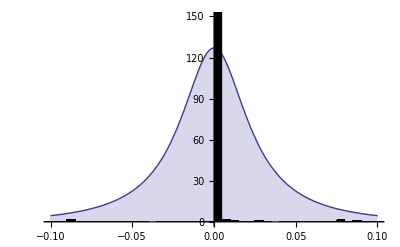

```mathematica
p[x]/.sol/.α->0.1/.u->0.0001/.σ->0.01;
Show[
Plot[%,{x,-0.1,0.1},PlotRange->{0,All},Filling->0],
Histogram[allreps,100,"PDF",ChartStyle->Black],
PlotRange->{{-0.1,0.1},{0,150}}
]
```

```mathematica
Clear[p]
```

```mathematica
p[z_,t_]:=p[z,t]=p[z,t-1]w[z]+u g[z]
```

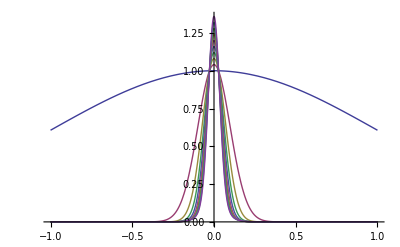

```mathematica
RecurrenceTable[{p[t+1]==p[t]w[z]+u g[z],p[0]==1},p,{t,1,1000,100}];
%/.u->0.0001/.α->0.1/.σ->1;
Plot[%,{z,-1,1},PlotRange->{0,All}]
```

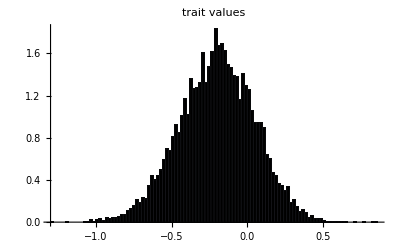

```mathematica
SetDirectory[NotebookDirectory[]]; 
Table[xs[i]=Import["../scripts/data/z_m1_N10000_alpha0.1_u0.0010_sigma0.010_rep"<>ToString[i]<>".csv"]//Flatten,{i,1}];
allreps=Table[xs[i],{i,1}]//Flatten;
Histogram[allreps,100,"PDF",ChartStyle->Black,PlotLabel->"trait distribution"]
```

## attempt #2 - ignore

Lets go straight to fitness.

We start with Martin & Lenormand’s (2016) PDF of selective effects

```mathematica
fs[s_,so_,λ_,n_]:=2/λ PDF[NoncentralChiSquareDistribution[n,(2so)/λ],2/λ(so-s)]HeavisideTheta[so-s];
```

where so = m_max-m_wt is the selection coefficient of the optimum phenotype, λ is the mutational variance per trait, and n is the number of traits under selection.

In our case we will have so=0, giving us a gamma distribution (see Martin & Lenormand 2006)

-(ⅇ^(s/λ) (-s/λ)^(n/2))/(s Gamma[n/2])

True

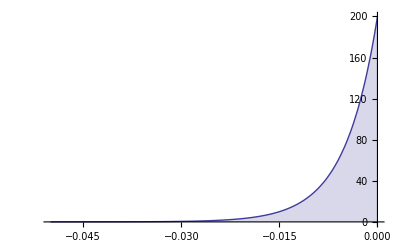

```mathematica
Simplify[fs[s,0,λ,n],{s<0,λ>0}]
%==Simplify[PDF[GammaDistribution[n/2,λ],-s],{s<0,λ>0}]
Plot[%%/.λ->0.005/.n->2,{s,-0.05,0},PlotRange->All,Filling->0]
```

Shift this to be the distribution of fitness

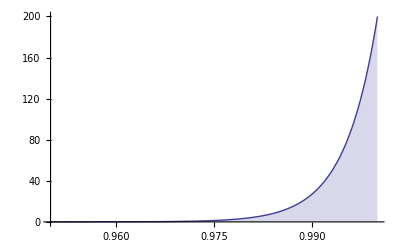

```mathematica
g[W_]:=Simplify[PDF[TransformedDistribution[1-s,s\[Distributed]GammaDistribution[n/2,λ]],W],{W<1,λ>0}]
Plot[g[W]/.λ->0.005/.n->2,{W,0.95,1},PlotRange->All,Filling->0]
```

Then at equilibrium, under the house-of-cards (HoC) approximation, the distribution of fitness is (Turelli 1984 eqn 3.2a)

```mathematica
p[W]==μ g[W]+(1-μ) W/Integrate[p[W]W,{W,0,1}] p[W]
sol=Solve[%,p[W]]

Simplify[%%/.%,{λ>0,n>0}]
Simplify[%/.μ->0.001/.n->2/.λ->0.005,1≥ W≥0]
```

p[W]==(ⅇ^((-1+W)/λ) (1-W)^(-1+n/2) λ^(-n/2) μ)/Gamma[n/2]+(W (1-μ) p[W])/(∫_0^1 W p[W]ⅆW)

{{p[W]→(-ⅇ^(-1/λ+W/λ) (1-W)^(n/2) λ^(-n/2) μ-2 W Gamma[n/2]+2 W^2 Gamma[n/2]+2 W μ Gamma[n/2]-2 W^2 μ Gamma[n/2])/(-Gamma[n/2]+W Gamma[n/2])}}

{(W (-1+μ) (ⅇ^(1/λ) (-1+W) λ^(n/2) (4+6 W (-1+μ)+(2-3 n λ) μ) Gamma[n/2]+3 μ (ⅇ^(W/λ) (1-W)^(n/2)-2 ⅇ^(1/λ) (-1+W) λ^(n/2) Gamma[n/2,1/λ]+2 ⅇ^(1/λ) (-1+W) λ^(1+n/2) Gamma[(2+n)/2,1/λ])))/((-1+W) ((-4+(-2+3 n λ) μ) Gamma[n/2]+6 μ (Gamma[n/2,1/λ]-λ Gamma[(2+n)/2,1/λ])))==0}

{-1/(-1.+W)5.40598×10^84 W (0.667663+ⅇ^(200. W) (-1.38528×10^-88+1.38528×10^-88 W)-1.66766 W+1. W^2)==0}

```mathematica
sol=Simplify[Solve[{p[W]==(μ g[W])/(1-k W)}/.k->(1-μ)/Integrate[p[W]W,{W,0,1}],p[W]],λ>0]
```

{{p[W]→0},{p[W]→(ⅇ^(-1/λ) λ^(-n/2) (-ⅇ^(W/λ) (1-W)^(n/2) μ-2 ⅇ^(1/λ) (-1+W) W λ^(n/2) (-1+μ) Gamma[n/2]))/((-1+W) Gamma[n/2])}}

```mathematica
(μ g[W])/(1-k W)/.k->Exp[-μ^2 π Vs/m^2]
%/.λ->0.005/.n->2/.μ->0.0001
(*Plot[,{W,0,1}]*)
```

(ⅇ^((-1+W)/λ) (1-W)^(-1+n/2) λ^(-n/2) μ)/((1-ⅇ^(-(π Vs μ^2)/m^2) W) Gamma[n/2])

(0.02 ⅇ^(200. (-1+W)))/(1-ⅇ^(-(3.14159×10^-8 Vs)/m^2) W)

Note that HoC requires the variance of new mutations to be much greater than that which exists (Turelli 1984 eqn 2.29).

Plot this equilibrium HoC distribution

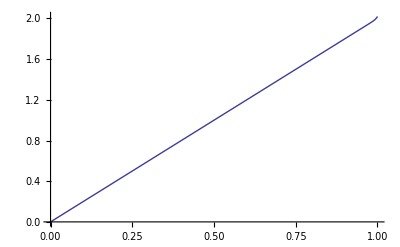

```mathematica
p[W]/.sol/.λ->0.005/.μ->0.0001/.n->2;
Plot[%,{W,0,1}]
```

again this weird linear thing

Check that the solution is good (trait distribution integrates to 1)

```mathematica
Integrate[p[W]/.sol,{W,0,1},Assumptions->{λ>0,n>0}]
%/.μ->0.0001/.n->2/.λ->0.005
```

{0,1-(μ Gamma[n/2,1/λ])/Gamma[n/2]}

{0,1.}

What is mean fitness at equilibrium?

```mathematica
Simplify[Integrate[p[W]W/.sol,{W,0,1}],{λ>0,n>0}]
%/.λ->0.005/.μ->0.0001/.n->2
```

{0,((4+(2-3 n λ) μ) Gamma[n/2]-6 μ (Gamma[n/2,1/λ]-λ Gamma[(2+n)/2,1/λ]))/(6 Gamma[n/2])}

{0,0.6667}

seems way too low

## attempt #3 - good

Neutral expectation

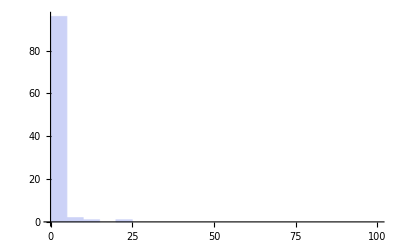

103.748

```mathematica
nplot=10^2;
θ Table[1/i,{i,1,nplot}]/.θ->2n u/.n->10^4/.u->10^-3;
Histogram[%,5,PlotRange->{{0,nplot},All}]
Total[%%]//N
```

Maybe I should focus more on alleles than traits? :

HoC? False

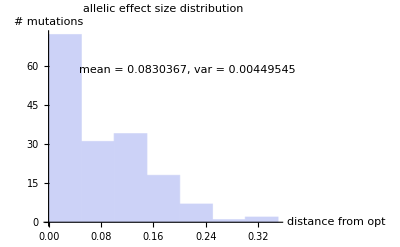

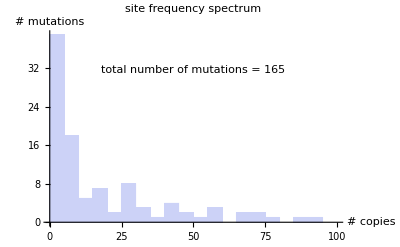

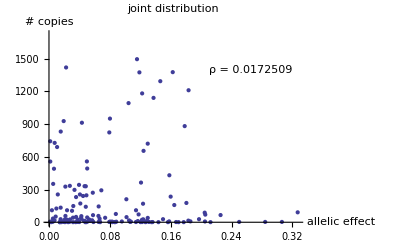

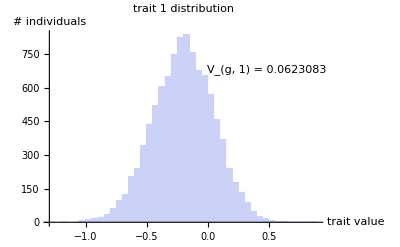

0.0316228

0.2

```mathematica
SetDirectory[NotebookDirectory[]]; 
Table[xs[i]=Import["../scripts/data/sgv_muts_m1_N10000_alpha0.1_u0.0010_sigma0.010_rep"<>ToString[i]<>".csv"],{i,1}];
effects=%[[1,1]];
copies=%%[[1,2]];

"HoC? "<>ToString[Simplify[u<α^2 σ<1]/.α->0.1/.u->0.001/.σ->0.01]

Histogram[effects,10,PlotLabel->"allelic effect size distribution",AxesLabel->{"distance from opt","# mutations"},Epilog->Inset[Text["mean = "<>ToString[Mean[effects]]<>", var = "<>ToString[Variance[effects]]],Scaled@{0.6,0.8}]]

Histogram[copies,1000,PlotRange->{{0,100},All},PlotLabel->"site frequency spectrum",AxesLabel->{"# copies","# mutations"},Epilog->Inset[Text["total number of mutations = "<>ToString[ Length[effects]]],Scaled@{0.5,0.8}]]

Table[{effects[[i]],copies[[i]]},{i,1,Length[effects]}];
ListPlot[%,PlotLabel->"joint distribution",AxesLabel->{"allelic effect","# copies"},Epilog->Inset[Text["ρ = "<>ToString[ Correlation[effects,copies]]],Scaled@{0.8,0.8}]]

traits=Import["../scripts/data/z_m1_N10000_alpha0.1_u0.0010_sigma0.010_rep1.csv"]//Flatten;
Histogram[Select[traits,#≠0&],PlotLabel->"trait 1 distribution",AxesLabel->{"trait value","# individuals"},Epilog->Inset[Text["V_(g, 1) = "<>ToString[ Variance[traits]]],Scaled@{0.8,0.8}]]
√(u α^2/σ)/.α->0.1/.u->0.001/.σ->0.01
2 u/σ/.α->0.1/.u->0.001/.σ->0.01
```

HoC? True

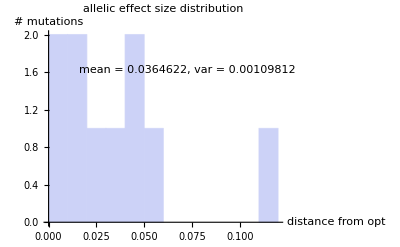

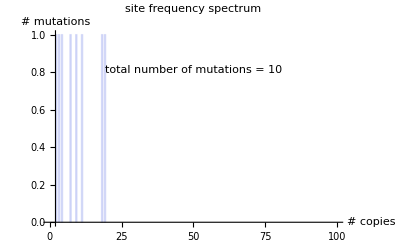

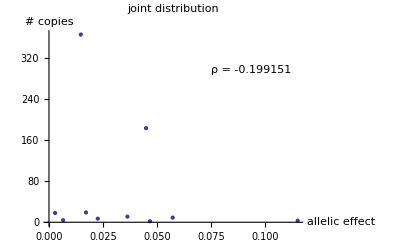

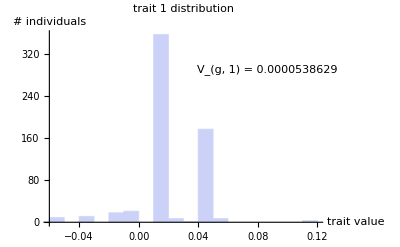

0.001

0.0002

```mathematica
SetDirectory[NotebookDirectory[]]; 
Table[xs[i]=Import["../scripts/data/sgv_muts_m1_N10000_alpha0.1_u0.0001_sigma1.000_rep"<>ToString[i]<>".csv"],{i,1}];
effects=%[[1,1]];
copies=%%[[1,2]];

"HoC? "<>ToString[Simplify[u<α^2 σ<1]/.α->0.1/.u->0.0001/.σ->1]

Histogram[effects,10,PlotLabel->"allelic effect size distribution",AxesLabel->{"distance from opt","# mutations"},Epilog->Inset[Text["mean = "<>ToString[Mean[effects]]<>", var = "<>ToString[Variance[effects]]],Scaled@{0.6,0.8}]]

Histogram[copies,1000,PlotRange->{{0,100},All},PlotLabel->"site frequency spectrum",AxesLabel->{"# copies","# mutations"},Epilog->Inset[Text["total number of mutations = "<>ToString[ Length[effects]]],Scaled@{0.5,0.8}]]

Table[{effects[[i]],copies[[i]]},{i,1,Length[effects]}];
ListPlot[%,PlotLabel->"joint distribution",AxesLabel->{"allelic effect","# copies"},Epilog->Inset[Text["ρ = "<>ToString[ Correlation[effects,copies]]],Scaled@{0.8,0.8}]]

traits=Import["../scripts/data/z_m1_N10000_alpha0.1_u0.0001_sigma1.000_rep1.csv"]//Flatten;
Histogram[Select[traits,#≠0&],PlotLabel->"trait 1 distribution",AxesLabel->{"trait value","# individuals"},Epilog->Inset[Text["V_(g, 1) = "<>ToString[ Variance[traits]]],Scaled@{0.8,0.8}]]
√(u α^2/σ)/.α->0.1/.u->0.0001/.σ->1
2 u/σ/.α->0.1/.u->0.0001/.σ->1
```

## multidimensional (see Turelli 1985 Genetics)

```mathematica
{u,α^2 σ}/.α->0.1/.u->0.001/.σ->0.01
```

{0.001,0.0001}

HoC? False

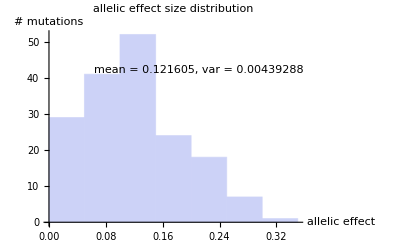

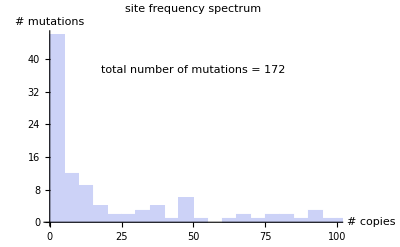

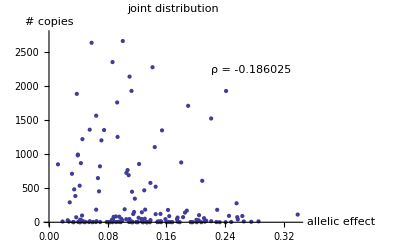

```mathematica
SetDirectory[NotebookDirectory[]]; 
Table[xs[i]=Import["../scripts/data/sgv_muts_n2_N10000_alpha0.1000_u0.0010_sigma0.0100_rep"<>ToString[i]<>".csv"],{i,1}];
effects=%[[1,1]];
copies=%%[[1,2]];

"HoC? "<>ToString[Simplify[u<α^2 σ<1]/.α->0.1/.u->0.001/.σ->0.01]

Histogram[effects,10,PlotLabel->"allelic effect size distribution",AxesLabel->{"allelic effect","# mutations"},Epilog->Inset[Text["mean = "<>ToString[Mean[effects]]<>", var = "<>ToString[Variance[effects]]],Scaled@{0.6,0.8}]]

Histogram[copies,1000,PlotRange->{{0,100},All},PlotLabel->"site frequency spectrum",AxesLabel->{"# copies","# mutations"},Epilog->Inset[Text["total number of mutations = "<>ToString[ Length[effects]]],Scaled@{0.5,0.8}]]

Table[{effects[[i]],copies[[i]]},{i,1,Length[effects]}];
ListPlot[%,PlotLabel->"joint distribution",AxesLabel->{"allelic effect","# copies"},Epilog->Inset[Text["ρ = "<>ToString[ Correlation[effects,copies]]],Scaled@{0.8,0.8}]]

traits=Import["../scripts/data/z_m2_N10000_alpha0.1_u0.0001_sigma1.000_rep1.csv"]//Flatten;
(*Histogram[Select[traits,#≠0&],PlotLabel->"trait 1 distribution",AxesLabel->{"trait value","# individuals"},Epilog->Inset[Text["V_(g, 1) = "<>ToString[ Variance[traits]]],Scaled@{0.8,0.8}]]
√(u α^2/σ)/.α->0.1/.u->0.0001/.σ->1
2 u/σ/.α->0.1/.u->0.0001/.σ->1*)
```

```mathematica
traits=Import["../test.txt"]//Flatten;
```

Flatten::normal: Nonatomic expression expected at position 1 in Flatten["1.000000000000000000e+00 2.000000000000000000e+00\n3.000000000000000000e+00 4.000000000000000000e+00"].

```mathematica
traits[[1]]
```

[ 0.  0.]

HoC? True

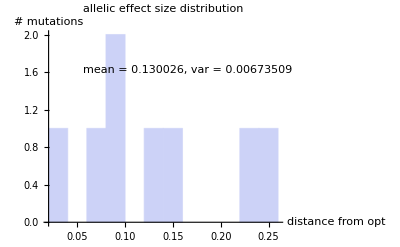

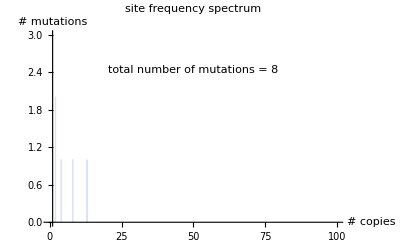

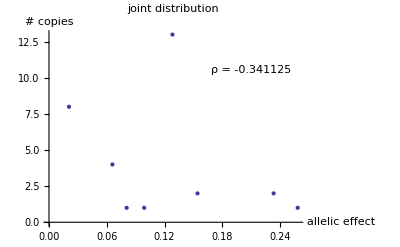

```mathematica
SetDirectory[NotebookDirectory[]]; 
Table[xs[i]=Import["../scripts/data/sgv_muts_m2_N10000_alpha0.1_u0.0001_sigma1.000_rep"<>ToString[i]<>".csv"],{i,1}];
effects=%[[1,1]];
copies=%%[[1,2]];

"HoC? "<>ToString[Simplify[u<α^2 σ<1]/.α->0.1/.u->0.0001/.σ->1]

Histogram[effects,10,PlotLabel->"allelic effect size distribution",AxesLabel->{"distance from opt","# mutations"},Epilog->Inset[Text["mean = "<>ToString[Mean[effects]]<>", var = "<>ToString[Variance[effects]]],Scaled@{0.6,0.8}]]

Histogram[copies,1000,PlotRange->{{0,100},All},PlotLabel->"site frequency spectrum",AxesLabel->{"# copies","# mutations"},Epilog->Inset[Text["total number of mutations = "<>ToString[ Length[effects]]],Scaled@{0.5,0.8}]]

Table[{effects[[i]],copies[[i]]},{i,1,Length[effects]}];
ListPlot[%,PlotLabel->"joint distribution",AxesLabel->{"allelic effect","# copies"},Epilog->Inset[Text["ρ = "<>ToString[ Correlation[effects,copies]]],Scaled@{0.8,0.8}]]

traits=Import["../scripts/data/z_m2_N10000_alpha0.1_u0.0001_sigma1.000_rep1.csv"]//Flatten;
(*Histogram[Select[traits,#≠0&],PlotLabel->"trait 1 distribution",AxesLabel->{"trait value","# individuals"},Epilog->Inset[Text["V_(g, 1) = "<>ToString[ Variance[traits]]],Scaled@{0.8,0.8}]]
√(u α^2/σ)/.α->0.1/.u->0.0001/.σ->1
2 u/σ/.α->0.1/.u->0.0001/.σ->1*)
```